```mathematica
Ntr=5.9375*10^6;
Nth=6.25*10^6;
T=Ntr/(Nth-Ntr)
```

19.

## VCSEL equations in terms of Q and ϕ

```mathematica
ClearAll["Global`*"];
eq1=κ(1+I α)(G+d-1)Fp-(γa+I γp)Fm+Sqrt[κ Csp (G+d+T)] (ξ1r+I ξ1i);
eq2=κ(1+I α)(G-d-1)Fm-(γa+I γp)Fp+Sqrt[κ Csp (G-d+T)] (ξ2r+I ξ2i);
eq3=γ(μ-G)-γ G(Abs[Fp]^2+Abs[Fm]^2)-γ d (Abs[Fp]^2-Abs[Fm]^2);
eq4=-γd d-γ G(Abs[Fp]^2-Abs[Fm]^2)-γ d (Abs[Fp]^2+Abs[Fm]^2);
```

```mathematica
Rsubs={Fp-> Fpr+I Fpi,Fm-> Fmr+I Fmi};Eq1=Expand[(eq1/.Rsubs)]//Re//FullSimplify[#,Assumptions->{_Symbol ∈Reals&&G+T+d>0&&κ>0&&Csp>0}]&;
Eq2=Expand[(eq1/.Rsubs)]//Im//FullSimplify[#,Assumptions->{_Symbol ∈Reals&&G+T+d>0&&κ>0&&Csp>0}]&;
Eq3=Expand[(eq2/.Rsubs)]//Re//FullSimplify[#,Assumptions->{_Symbol ∈Reals&&G+T-d>0&&κ>0&&Csp>0}]&;
Eq4=Expand[(eq2/.Rsubs)]//Im//FullSimplify[#,Assumptions->{_Symbol ∈Reals&&G+T-d>0&&κ>0&&Csp>0}]&;
Eqs={Eq1,Eq2,Eq3,Eq4};
```

```mathematica
Eqvars={Fpr,Fpi,Fmr,Fmi};
Eqnoise={ξ1r,ξ1i,ξ2r,ξ2i};
Coefs=Table[CoefficientList[Eqs[[i]],Eqnoise[[i]]],{i,1,4}];
```

```mathematica
Qvarexpl={Fpr^2+Fpi^2,ArcTan[Fpi/Fpr]-ω t,Fmr^2+Fmi^2,ArcTan[Fmi/Fmr]-ω t};
EqQ=Table[D[Qvarexpl[[i]],t]+Sum[D[Qvarexpl[[i]],Eqvars[[j]]] Coefs[[j,1]],{j,1,4}]+1/2 Sum[D[Qvarexpl[[i]],{Eqvars[[j]],2}]Coefs[[j,2]]^2,{j,1,4}],{i,1,4}]//FullSimplify;
FfQsub={Fpr-> Sqrt[Qp]*Cos[ϕp+ωt],Fpi-> Sqrt[Qp]*Sin[ϕp+ωt],Fmr-> Sqrt[Qm]*Cos[ϕm+ωt],Fmi-> Sqrt[Qm]*Sin[ϕm+ωt]};
EqQsimple=EqQ/.FfQsub//FullSimplify[#,Assumptions->{Qm>0&&Qp>0}]&;
EqQdiff=Table[Sum[D[Qvarexpl[[i]],Eqvars[[j]]] Coefs[[j,2]] Eqnoise[[j]],{j,1,4}],{i,1,4}]/.FfQsub//FullSimplify[#,Assumptions->{Qm>0&&Qp>0}]&;
EqQsimple/.{ϕm-ϕp-> -2ψ}//FullSimplify//MatrixForm
```

(2 ((-1+d+G) Qp κ+Csp (d+G+T) κ-√(Qm Qp) (γa Cos[2 ψ]+γp Sin[2 ψ]))
(-1+d+G) α κ-ω+√(Qm/Qp) (-γp Cos[2 ψ]+γa Sin[2 ψ])
-2 ((Qm+(d-G) (Csp+Qm)-Csp T) κ+√(Qm Qp) (γa Cos[2 ψ]-γp Sin[2 ψ]))
(-1-d+G) α κ-ω-(Qp (γp Cos[2 ψ]+γa Sin[2 ψ]))/(√(Qm Qp)))

```mathematica
Dmatrix=(KroneckerProduct[EqQdiff,EqQdiff]//Expand)/.({Table[Eqnoise[[i]] Eqnoise[[j]]-> KroneckerDelta[i,j],{i,1,4},{j,1,4}],Table[Eqnoise[[i]]-> 0,{i,1,4}]}//Flatten)//FullSimplify;
Dmatrix//MatrixForm
```

(4 Csp Qp (d+G+T) κ | 0 | 0 | 0
0 | (Csp (d+G+T) κ)/Qp | 0 | 0
0 | 0 | 4 Csp Qm (-d+G+T) κ | 0
0 | 0 | 0 | (Csp (-d+G+T) κ)/Qm)

```mathematica
{Table[Eqnoise[[i]] Eqnoise[[j]]-> KroneckerDelta[i,j],{i,1,4},{j,1,4}],Table[Eqnoise[[i]]-> 0,{i,1,4}]}//Flatten
```

{ξ1r^2→1,ξ1i ξ1r→0,ξ1r ξ2r→0,ξ1r ξ2i→0,ξ1i ξ1r→0,ξ1i^2→1,ξ1i ξ2r→0,ξ1i ξ2i→0,ξ1r ξ2r→0,ξ1i ξ2r→0,ξ2r^2→1,ξ2i ξ2r→0,ξ1r ξ2i→0,ξ1i ξ2i→0,ξ2i ξ2r→0,ξ2i^2→1,ξ1r→0,ξ1i→0,ξ2r→0,ξ2i→0}

```mathematica
EqQs={EqQsimple,{eq3,eq4}/.Rsubs/.FfQsub//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&_Symbol∈Reals}]&}//Flatten;
EqQs[[1]]=EqQsimple[[1]];
EqQs[[2]]=EqQsimple[[3]];
EqQs[[3]]=(EqQsimple[[2]]+EqQsimple[[4]])/2//FullSimplify;
EqQs[[4]]=(EqQsimple[[2]]-EqQsimple[[4]])/2//FullSimplify;
EqQs=EqQs/.{ϕm-ϕp->- 2ψ}//FullSimplify;
```

```mathematica
EqQs//MatrixForm
```

(2 ((-1+d+G) Qp κ+Csp (d+G+T) κ-√(Qm Qp) (γa Cos[2 ψ]+γp Sin[2 ψ]))
-2 ((Qm+(d-G) (Csp+Qm)-Csp T) κ+√(Qm Qp) (γa Cos[2 ψ]-γp Sin[2 ψ]))
-(2 Qm (α κ-G α κ+ω)+(Qm √(Qm/Qp)+√(Qm Qp)) γp Cos[2 ψ]+(-Qm √(Qm/Qp)+√(Qm Qp)) γa Sin[2 ψ])/(2 Qm)
(2 d Qm α κ+(-Qm √(Qm/Qp)+√(Qm Qp)) γp Cos[2 ψ]+(Qm √(Qm/Qp)+√(Qm Qp)) γa Sin[2 ψ])/(2 Qm)
-γ (d (-Qm+Qp)+G (1+Qm+Qp)-μ)
G (Qm-Qp) γ-d ((Qm+Qp) γ+γd))

```mathematica
EqQs[[1]]-EqQs[[2]]//FullSimplify
```

2 (2 Csp d+(1+d-G) Qm+(-1+d+G) Qp) κ-4 √(Qm Qp) γp Sin[2 ψ]

## Linearization

```mathematica
EqQs={EqQsimple,{eq3,eq4}/.Rsubs/.FfQsub//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&_Symbol∈Reals}]&}//Flatten;
EqQs[[1]]=EqQsimple[[1]];
EqQs[[2]]=EqQsimple[[3]];
EqQs[[3]]=(EqQsimple[[2]]+EqQsimple[[4]])/2//FullSimplify;
EqQs[[4]]=(EqQsimple[[2]]-EqQsimple[[4]])/2//FullSimplify;
EqQs=EqQs/.{ϕm-ϕp->- 2ψ}//FullSimplify;
deltas={δQp,δQm,δϕ,δψ,Δ,δ};
vars={Qp,Qm,ϕ,ψ,G,d};
semilinsubs=Table[vars[[i]]-> vars[[i]]+deltas[[i]],{i,1,6}];
```

```mathematica
M=Table[D[EqQs[[i]],vars[[j]]],{i,1,6},{j,1,6}]//FullSimplify[#,Assumptions-> {Qp>0&&Qm>0}]&;
(*M=Drop[M,{3},{3}];*)
M//MatrixForm
```

(2 (-1+d+G) κ-(Qm (γa Cos[2 ψ]+γp Sin[2 ψ]))/(√(Qm Qp)) | -(Qp (γa Cos[2 ψ]+γp Sin[2 ψ]))/(√(Qm Qp)) | 0 | 4 √(Qm Qp) (-γp Cos[2 ψ]+γa Sin[2 ψ]) | 2 (Csp+Qp) κ | 2 (Csp+Qp) κ
(Qm (-γa Cos[2 ψ]+γp Sin[2 ψ]))/(√(Qm Qp)) | -2 (1+d-G) κ+(Qp (-γa Cos[2 ψ]+γp Sin[2 ψ]))/(√(Qm Qp)) | 0 | 4 √(Qm Qp) (γp Cos[2 ψ]+γa Sin[2 ψ]) | 2 (Csp+Qm) κ | -2 (Csp+Qm) κ
-((-Qm √(Qm Qp)+√(Qm Qp^3)) γp Cos[2 ψ]+(√(Qm^3 Qp)+√(Qm Qp^3)) γa Sin[2 ψ])/(4 Qm Qp^2) | ((-Qm √(Qm Qp)+√(Qm Qp^3)) γp Cos[2 ψ]+(√(Qm^3 Qp)+√(Qm Qp^3)) γa Sin[2 ψ])/(4 Qm^2 Qp) | 0 | ((Qm-Qp) γa Cos[2 ψ]+(Qm+Qp) γp Sin[2 ψ])/(√(Qm Qp)) | α κ | 0
((√(Qm^3 Qp)+√(Qm Qp^3)) γp Cos[2 ψ]+(-Qm √(Qm Qp)+√(Qm Qp^3)) γa Sin[2 ψ])/(4 Qm Qp^2) | (-(√(Qm^3 Qp)+√(Qm Qp^3)) γp Cos[2 ψ]+(√(Qm^3 Qp)-√(Qm Qp^3)) γa Sin[2 ψ])/(4 Qm^2 Qp) | 0 | ((Qm+Qp) γa Cos[2 ψ]+(Qm-Qp) γp Sin[2 ψ])/(√(Qm Qp)) | 0 | α κ
-(d+G) γ | (d-G) γ | 0 | 0 | -(1+Qm+Qp) γ | (Qm-Qp) γ
-(d+G) γ | (-d+G) γ | 0 | 0 | (Qm-Qp) γ | -(Qm+Qp) γ-γd)

## Linear polarization

```mathematica
linEqs=EqQs/.{Qp->Q,Qm-> Q}//FullSimplify[#,Assumptions->Q>0]&;
linEqs//MatrixForm
```

(2 ((-1+d+G) Q κ+Csp (d+G+T) κ-Q (γa Cos[2 ψ]+γp Sin[2 ψ]))
-2 ((Q+(d-G) (Csp+Q)-Csp T) κ+Q γa Cos[2 ψ]-Q γp Sin[2 ψ])
(-1+G) α κ-ω-γp Cos[2 ψ]
d α κ+γa Sin[2 ψ]
γ (-G (1+2 Q)+μ)
-d (2 Q γ+γd))

```mathematica
(* d=0, ψ=0 (x-polarization) so*)
linEqs=linEqs/.{d-> 0,ψ-> 0}//FullSimplify;
linEqs//MatrixForm
```

(2 Csp (G+T) κ-2 Q (γa+κ-G κ)
2 Csp (G+T) κ-2 Q (γa+κ-G κ)
-γp+(-1+G) α κ-ω
0
γ (-G (1+2 Q)+μ)
0)

```mathematica
Gxsub=Solve[linEqs[[1]]==0,G][[1]]
Qxsub=Solve[(linEqs[[5]]/.Gxsub//FullSimplify)==0,Q][[2]]
```

{G→(Q γa+Q κ-Csp T κ)/((Csp+Q) κ)}

{Q→(γa+κ-2 Csp T κ-κ μ+√((-γa-κ+2 Csp T κ+κ μ)^2-4 (-2 γa-2 κ) (Csp T κ+Csp κ μ)))/(2 (-2 γa-2 κ))}

```mathematica
tmp=M/.{d-> 0,ψ-> 0,Qp->Q,Qm-> Q}/.Qxsub//FullSimplify[#,Assumptions->{Q>0}]&;
tmp//MatrixForm
```

(2 (-1+G) κ+(γa (γa+κ) √(((γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^2)/(γa+κ)^2))/(γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2)) | (γa (γa+κ) √(((γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^2)/(γa+κ)^2))/(γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2)) | 0 | -γp √(((γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^2)/(γa+κ)^2) | (κ ((-1+4 Csp) γa+κ (-1+2 Csp (2+T)+μ)-√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2)))/(2 (γa+κ)) | (κ ((-1+4 Csp) γa+κ (-1+2 Csp (2+T)+μ)-√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2)))/(2 (γa+κ))
(γa (γa+κ) √(((γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^2)/(γa+κ)^2))/(γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2)) | 2 (-1+G) κ+(γa (γa+κ) √(((γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^2)/(γa+κ)^2))/(γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2)) | 0 | γp √(((γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^2)/(γa+κ)^2) | (κ ((-1+4 Csp) γa+κ (-1+2 Csp (2+T)+μ)-√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2)))/(2 (γa+κ)) | (κ (γa-4 Csp γa+κ-4 Csp κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2)))/(2 (γa+κ))
(γp (((γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^3)/(√(((γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^2)/(γa+κ)^2))+(γa+κ)^3 √(((γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^4)/(γa+κ)^4)))/((γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^3) | -(γp (((γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^3)/(√(((γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^2)/(γa+κ)^2))+(γa+κ)^3 √(((γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^4)/(γa+κ)^4)))/((γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^3) | 0 | 0 | α κ | 0
-(2 γp (γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2)))/((γa+κ) √(((γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^4)/(γa+κ)^4)) | (2 γp (γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2)))/((γa+κ) √(((γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^4)/(γa+κ)^4)) | 0 | -(2 γa (γa+κ) √(((γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^2)/(γa+κ)^2))/(γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2)) | 0 | α κ
-G γ | -G γ | 0 | 0 | -(γ (γa+κ+2 Csp T κ+κ μ-√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2)))/(2 (γa+κ)) | 0
-G γ | G γ | 0 | 0 | 0 | (γa (γ-2 γd)-2 γd κ-γ κ (-1+2 Csp T+μ)+γ √(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))/(2 (γa+κ)))

```mathematica
mat1={
{1/(2Sqrt[Qp]),1/(2Sqrt[Qm]),I Sqrt[Qp]+I Sqrt[Qm],I Sqrt[Qp]-I Sqrt[Qm],0,0},
{1/(2Sqrt[Qp]),1/(2Sqrt[Qm]),-I Sqrt[Qp]-I Sqrt[Qm],-I Sqrt[Qp]+I Sqrt[Qm],0,0},
{0,0,0,0,1,0},
{1/(2Sqrt[Qp]),-1/(2Sqrt[Qm]),I Sqrt[Qp]-I Sqrt[Qm],I Sqrt[Qp]+I Sqrt[Qm],0,0},
{1/(2Sqrt[Qp]),-1/(2Sqrt[Qm]),-I Sqrt[Qp]+I Sqrt[Qm],-I Sqrt[Qp]-I Sqrt[Qm],0,0},
{0,0,0,0,0,1}};
linMapam=mat1.M.Inverse[mat1]/.{Qp->Q,Qm->Q,d->0,ψ-> 0}/.Gxsub//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&Q>0}]&;
linMapam//MatrixForm
```

(-(Csp (γa+κ+T κ))/(Csp+Q) | -(Csp (γa+κ+T κ))/(Csp+Q) | (2 (Csp+Q+ⅈ Q α) κ)/(√Q) | 0 | 0 | 0
-(Csp (γa+κ+T κ))/(Csp+Q) | -(Csp (γa+κ+T κ))/(Csp+Q) | (2 (Csp+Q-ⅈ Q α) κ)/(√Q) | 0 | 0 | 0
-(√Q γ (-Csp T κ+Q (γa+κ)))/((Csp+Q) κ) | -(√Q γ (-Csp T κ+Q (γa+κ)))/((Csp+Q) κ) | -(1+2 Q) γ | 0 | 0 | 0
0 | 0 | 0 | (2 Q (γa+ⅈ γp)+Csp (γa+2 ⅈ γp-(1+T) κ))/(Csp+Q) | -(Csp (γa+κ+T κ))/(Csp+Q) | (2 (Csp+Q+ⅈ Q α) κ)/(√Q)
0 | 0 | 0 | -(Csp (γa+κ+T κ))/(Csp+Q) | (2 Q (γa-ⅈ γp)+Csp (γa-2 ⅈ γp-(1+T) κ))/(Csp+Q) | (2 (Csp+Q-ⅈ Q α) κ)/(√Q)
0 | 0 | 0 | -(√Q γ (-Csp T κ+Q (γa+κ)))/((Csp+Q) κ) | -(√Q γ (-Csp T κ+Q (γa+κ)))/((Csp+Q) κ) | -2 Q γ-γd)

```mathematica
linM1=linMapam[[1;;3,1;;3]];
linM2=linMapam[[4;;6,4;;6]];
```

```mathematica
c1=Reverse[CharacteristicPolynomial[linM1,λ]*(-1)//CoefficientList[#,λ]&]//FullSimplify;
c2=Reverse[CharacteristicPolynomial[linM2,λ]*(-1)//CoefficientList[#,λ]&]//FullSimplify;
c1//MatrixForm
c2//MatrixForm
```

(1
(Q (1+2 Q) γ+Csp (γ+2 Q γ+2 (γa+κ+T κ)))/(Csp+Q)
(2 γ (-2 Csp^2 T κ+2 Q^2 (γa+κ)+Csp (γa+4 Q γa+(1+4 Q+T) κ)))/(Csp+Q)
0)

(1
(Q (2 Q γ-4 γa+γd)+Csp (2 Q γ-2 γa+γd+2 (1+T) κ))/(Csp+Q)
(4 Q^2 γ (-γa+κ)+4 Q (γa^2-γa γd+γp^2+2 Csp γ κ)+2 Csp (-γa γd+(1+T) (-2 γa+γd) κ+2 (γp^2-Csp T γ κ)))/(Csp+Q)
(8 Csp^2 T γ γa κ+4 Q (γa^2 γd-2 Q γ γa (α γp+κ)+γp (γd γp+2 Q γ (γp-α κ)))-4 Csp (-γd γp^2+(1+T) γa γd κ+2 Q γ (γa^2+2 γa κ-γp (γp+T α κ))))/(Csp+Q))

```mathematica
c2eq=c2[[2]]*c2[[3]]-c2[[4]]//FullSimplify;
```

```mathematica
c1simpl=c1/.Qxsub//FullSimplify;
c2simpl=c2/.Qxsub//FullSimplify;
c2eqsimpl=c2eq/.Qxsub//FullSimplify;
```

$Aborted

```mathematica
γ=1.;
γa=-0.1;
γa1=γa;
γd=50.;
α=5.;
κ=300.;
Ntr=5.9375*10^6;
Nth=6.25*10^6;
Csp=0;
(*Csp=0;*)
T=Ntr/(Nth-Ntr);
(*sol1=Solve[c2simpl[[4]]==0,μ];*)
(*sol2=Solve[c2eqsimpl==0,μ];*)
γpmin=0.01;
γpmax=100;
Nγp=1000;
```

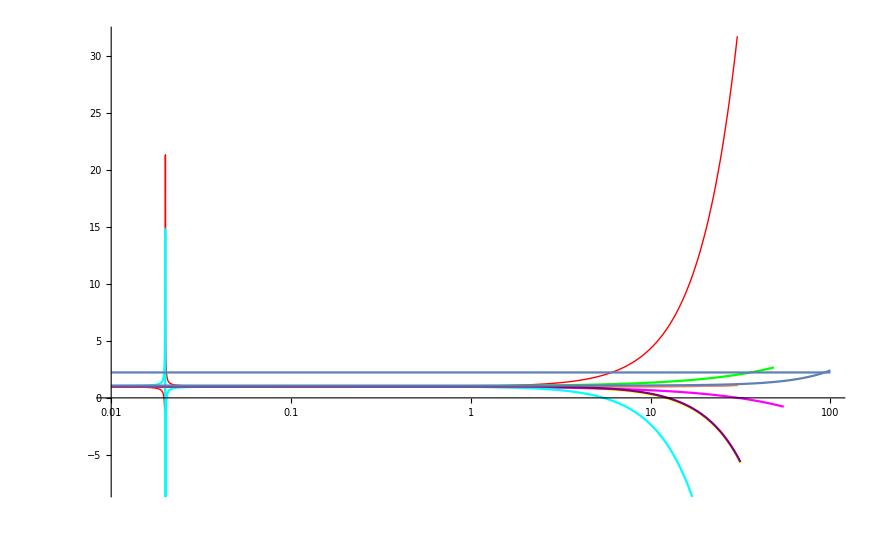

```mathematica
Clear[γp,γa];
p1=LogLinearPlot[μ/.solC3[[1]]/.{γa-> γa1},{γp,0.01,100},PlotStyle->{Red,Thick}];
p2=LogLinearPlot[μ/.solC3[[2]]/.{γa-> γa1},{γp,0.01,100},PlotStyle->Green];
p21=LogLinearPlot[μ/.solC2[[1]]/.{γa-> γa1},{γp,0.01,100},PlotStyle->{Orange}];
p22=LogLinearPlot[μ/.solC2[[2]]/.{γa-> γa1},{γp,0.01,100},PlotStyle->Yellow];
p1y=LogLinearPlot[μ/.solC3[[1]]/.{γp-> -x,γa-> -γa1},{x,0.01,100},PlotStyle->Magenta];
p2y=LogLinearPlot[μ/.solC3[[2]]/.{γp-> -x,γa-> -γa1},{x,0.01,100},PlotStyle->Cyan];
p21y=LogLinearPlot[μ/.solC2[[1]]/.{γp-> -x,γa-> -γa1},{x,0.01,100},PlotStyle->{Pink}];
p22y=LogLinearPlot[μ/.solC2[[2]]/.{γp-> -x,γa-> -γa1},{x,0.01,100},PlotStyle->Purple];
Show[p1,p2,p21,p22,p1y,p2y,p21y,p22y,lpx,lpy]
```

```mathematica
Log[100]//N
```

4.60517

```mathematica
solC3=Solve[(c2simpl[[4]])==0,μ]//Simplify;
```

```mathematica
solC2=Solve[(c2simpl[[3]])==0,μ]//Simplify;
```

```mathematica
solC3
```

{{μ→-((γa^4 γd^2 κ+α γ γa^3 γd γp κ-γ γa^2 γd γp^2 κ+γa^2 γd^2 γp^2 κ-α γ γa γd γp^3 κ+γ γd γp^4 κ+γ γa^3 γd κ^2+γa^3 γd^2 κ^2+3 α γ γa^2 γd γp κ^2-3 γ γa γd γp^2 κ^2+γa γd^2 γp^2 κ^2-α γ γd γp^3 κ^2+2 γ γa^2 γd κ^3+2 α γ γa γd γp κ^3+4 Csp^2 γ^2 κ (γa^4+4 γa^3 κ-2 (2+T) γa γp^2 κ+γp^3 (γp+T α κ)+γa^2 (-2 γp^2+T α γp κ+2 (2+T) κ^2))-2 Csp γ κ (2 γa^4 γd+γa^3 (α γ γp+(γ+5 γd) κ)+γp^2 (γd γp (γp-2 α κ)+γ (γp-α κ) (γp-T α κ))+γa^2 (γ (-γp^2+3 α γp κ+2 κ^2)+γd (-γp^2+(2+T) α γp κ+2 (2+T) κ^2))+γa γp (T α^2 γ γp κ-(3 γ+(3+2 T) γd) γp κ+α (-γ γp^2-2 γd γp^2+(2+T) γ κ^2+(2+T) γd κ^2)))-√(κ^2 (γa^2 γd+α γ γa γp+γa (γ+γd) κ+γ γp (-γp+α κ)-2 Csp γ (γa^2-γp^2+2 γa κ))^2 (γd^2 (γa^2+γp^2)^2+4 Csp^2 γ^2 (γa^4+4 γa^3 κ-4 (1+T) γa γp^2 κ+γp^2 (γp+T α κ)^2+γa^2 (-2 γp^2+2 T α γp κ+4 (1+T) κ^2))-4 Csp γ γd (γa^4+2 γa^3 κ+γa^2 κ ((2+T) α γp+2 (1+T) κ)+γp^3 (γp-(2+T) α κ)-2 γa γp ((1+T) γp κ+α (γp^2-(1+T) κ^2))))))/(2 γ (-γa γd+2 Csp γ (γa-α γp)) κ^2 (-γp^2+γa κ+α γp (γa+κ))))},{μ→-((γa^4 γd^2 κ+α γ γa^3 γd γp κ-γ γa^2 γd γp^2 κ+γa^2 γd^2 γp^2 κ-α γ γa γd γp^3 κ+γ γd γp^4 κ+γ γa^3 γd κ^2+γa^3 γd^2 κ^2+3 α γ γa^2 γd γp κ^2-3 γ γa γd γp^2 κ^2+γa γd^2 γp^2 κ^2-α γ γd γp^3 κ^2+2 γ γa^2 γd κ^3+2 α γ γa γd γp κ^3+4 Csp^2 γ^2 κ (γa^4+4 γa^3 κ-2 (2+T) γa γp^2 κ+γp^3 (γp+T α κ)+γa^2 (-2 γp^2+T α γp κ+2 (2+T) κ^2))-2 Csp γ κ (2 γa^4 γd+γa^3 (α γ γp+(γ+5 γd) κ)+γp^2 (γd γp (γp-2 α κ)+γ (γp-α κ) (γp-T α κ))+γa^2 (γ (-γp^2+3 α γp κ+2 κ^2)+γd (-γp^2+(2+T) α γp κ+2 (2+T) κ^2))+γa γp (T α^2 γ γp κ-(3 γ+(3+2 T) γd) γp κ+α (-γ γp^2-2 γd γp^2+(2+T) γ κ^2+(2+T) γd κ^2)))+√(κ^2 (γa^2 γd+α γ γa γp+γa (γ+γd) κ+γ γp (-γp+α κ)-2 Csp γ (γa^2-γp^2+2 γa κ))^2 (γd^2 (γa^2+γp^2)^2+4 Csp^2 γ^2 (γa^4+4 γa^3 κ-4 (1+T) γa γp^2 κ+γp^2 (γp+T α κ)^2+γa^2 (-2 γp^2+2 T α γp κ+4 (1+T) κ^2))-4 Csp γ γd (γa^4+2 γa^3 κ+γa^2 κ ((2+T) α γp+2 (1+T) κ)+γp^3 (γp-(2+T) α κ)-2 γa γp ((1+T) γp κ+α (γp^2-(1+T) κ^2))))))/(2 γ (-γa γd+2 Csp γ (γa-α γp)) κ^2 (-γp^2+γa κ+α γp (γa+κ))))}}

```mathematica
c2simpl[[4]]/.{Csp->0}/.tmpsol
```

{4 (γa^2 γd+1/(2 (γa+κ))γ γa (α γp+κ) (γa+κ-(γa γd^2 (γa^2+γp^2) κ (γa+κ)+γ γd κ (γa^2-γp^2+2 γa κ) (-γp^2+γa κ+α γp (γa+κ))-√(γd^2 (γa^2+γp^2)^2 κ^2 (γa^2 γd+α γ γa γp+γa (γ+γd) κ+γ γp (-γp+α κ))^2))/(2 γ γa γd κ (-γp^2+γa κ+α γp (γa+κ)))+√(γa-κ (-1+(γa γd^2 (γa^2+γp^2) κ (γa+κ)+γ γd κ (γa^2-γp^2+2 γa κ) (-γp^2+γa κ+α γp (γa+κ))-√(γd^2 (γa^2+γp^2)^2 κ^2 (γa^2 γd+α γ γa γp+γa (γ+γd) κ+γ γp (-γp+α κ))^2))/(2 γ γa γd κ^2 (-γp^2+γa κ+α γp (γa+κ)))))^2)+γp (γd γp+1/(2 (γa+κ))γ (-γp+α κ) (γa+κ-(γa γd^2 (γa^2+γp^2) κ (γa+κ)+γ γd κ (γa^2-γp^2+2 γa κ) (-γp^2+γa κ+α γp (γa+κ))-√(γd^2 (γa^2+γp^2)^2 κ^2 (γa^2 γd+α γ γa γp+γa (γ+γd) κ+γ γp (-γp+α κ))^2))/(2 γ γa γd κ (-γp^2+γa κ+α γp (γa+κ)))+√(γa-κ (-1+(γa γd^2 (γa^2+γp^2) κ (γa+κ)+γ γd κ (γa^2-γp^2+2 γa κ) (-γp^2+γa κ+α γp (γa+κ))-√(γd^2 (γa^2+γp^2)^2 κ^2 (γa^2 γd+α γ γa γp+γa (γ+γd) κ+γ γp (-γp+α κ))^2))/(2 γ γa γd κ^2 (-γp^2+γa κ+α γp (γa+κ)))))^2))),4 (γa^2 γd+1/(2 (γa+κ))γ γa (α γp+κ) (γa+κ-(γa γd^2 (γa^2+γp^2) κ (γa+κ)+γ γd κ (γa^2-γp^2+2 γa κ) (-γp^2+γa κ+α γp (γa+κ))+√(γd^2 (γa^2+γp^2)^2 κ^2 (γa^2 γd+α γ γa γp+γa (γ+γd) κ+γ γp (-γp+α κ))^2))/(2 γ γa γd κ (-γp^2+γa κ+α γp (γa+κ)))+√(γa-κ (-1+(γa γd^2 (γa^2+γp^2) κ (γa+κ)+γ γd κ (γa^2-γp^2+2 γa κ) (-γp^2+γa κ+α γp (γa+κ))+√(γd^2 (γa^2+γp^2)^2 κ^2 (γa^2 γd+α γ γa γp+γa (γ+γd) κ+γ γp (-γp+α κ))^2))/(2 γ γa γd κ^2 (-γp^2+γa κ+α γp (γa+κ)))))^2)+γp (γd γp+1/(2 (γa+κ))γ (-γp+α κ) (γa+κ-(γa γd^2 (γa^2+γp^2) κ (γa+κ)+γ γd κ (γa^2-γp^2+2 γa κ) (-γp^2+γa κ+α γp (γa+κ))+√(γd^2 (γa^2+γp^2)^2 κ^2 (γa^2 γd+α γ γa γp+γa (γ+γd) κ+γ γp (-γp+α κ))^2))/(2 γ γa γd κ (-γp^2+γa κ+α γp (γa+κ)))+√(γa-κ (-1+(γa γd^2 (γa^2+γp^2) κ (γa+κ)+γ γd κ (γa^2-γp^2+2 γa κ) (-γp^2+γa κ+α γp (γa+κ))+√(γd^2 (γa^2+γp^2)^2 κ^2 (γa^2 γd+α γ γa γp+γa (γ+γd) κ+γ γp (-γp+α κ))^2))/(2 γ γa γd κ^2 (-γp^2+γa κ+α γp (γa+κ)))))^2)))}

```mathematica
((μ/.tmpsol[[1]])-(μ/.tmpsol[[2]])//FullSimplify[#,Assumptions->γp>0&&γa∈Reals&&κ>0&&γd>0&&α>0&&γ>0]&)
```

-(0.0333333 (0.01+γp^2) Abs[1529.5+γp (-1499.5+1. γp)])/(30.+(-1499.5+γp) γp)

```mathematica
Clear[γp]
```

```mathematica
eqy
```

-30242.3+6002. γp-1.6 γp^2-1.81899×10^-11 √((1.00033-1. μ)^2)+9.09495×10^-13 γp √((1.00033-1. μ)^2)+(28641.-6000. γp) μ+599.4 μ^2+(-4.36679×10^-11+1.8196×10^-12 γp-1.28786×10^-14 γp^2-3.63798×10^-11 √((1.00033-1. μ)^2)-1.81899×10^-12 γp √((1.00033-1. μ)^2)-2.55351×10^-14 γp^2 √((1.00033-1. μ)^2)+3.63919×10^-11 μ-1.8196×10^-12 γp μ-1.81899×10^-11 μ^2+9.09495×10^-13 γp μ^2)/(-1.00033-1. √((1.00033-1. μ)^2)+1. μ)

```mathematica
eqx
```

-28541.9-5998. γp+1.6 γp^2+1.81899×10^-11 √((0.999667-1. μ)^2)-9.09495×10^-13 γp √((0.999667-1. μ)^2)+(28959.4+6000. γp) μ+600.6 μ^2+(1.81778×10^-11-1.81838×10^-12 γp+1.19904×10^-14 γp^2+3.63798×10^-12 √((0.999667-1. μ)^2)-1.81899×10^-12 γp √((0.999667-1. μ)^2)-2.19824×10^-14 γp^2 √((0.999667-1. μ)^2)-3.63677×10^-11 μ+1.81838×10^-12 γp μ+1.81899×10^-11 μ^2-9.09495×10^-13 γp μ^2)/(-0.999667-1. √((0.999667-1. μ)^2)+1. μ)

```mathematica
ContourPlot[eqx==0,{γp,γpmin,γpmax},{μ,1,10},PlotPoints->100]
```

-Graphics-

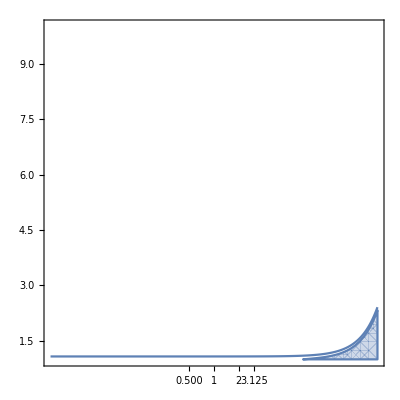

```mathematica
Show[rp,lp]
```

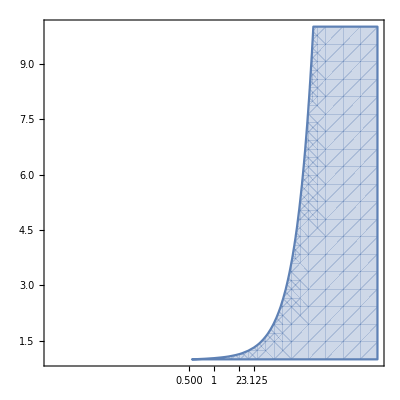

```mathematica
rp=RegionPlot[(c2simpl[[4]]/.{γp-> Power[10,x]})>0,{x,Log10[γpmin],Log10[γpmax]},{μ,1,10},FrameTicks->{Automatic,{Charting`ScaledTicks[{Log10,Exp}],None}}]
```

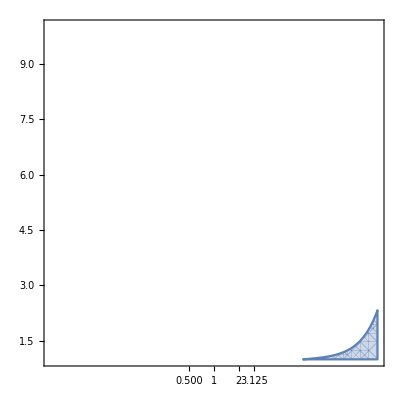

```mathematica
rp=RegionPlot[(c2simpl[[3]]/.{γp-> Power[10,x]})>0,{x,Log10[γpmin],Log10[γpmax]},{μ,1,10},FrameTicks->{Automatic,{Charting`ScaledTicks[{Log10,Exp}],None}}]
```

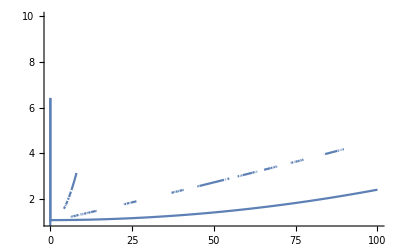

```mathematica
Show[p1,p2,p3,lp,ScalingFunctions->{"Log10",None},PlotRange->{{0.1,100},{1,10}}]
```

```mathematica
Clear[γ,γa,γp,γd,α,κ,μ,T,Ntr,Nth,Csp,γpmin,γpmax];
```

```mathematica
Clear[γp]
```

```mathematica
c2eqsimpl//FullSimplify
```

1/(1.15878×10^9+1. μ)μ^3 (-3584. √(90008.4+μ (-179864.+90000. μ))+μ (-1.04858×10^6-256. μ^2+251. √(90008.4+μ (-179864.+90000. μ))-0.5 μ √(90008.4+μ (-179864.+90000. μ))))

```mathematica
c2eqsimpl
```

(-(8 Csp (γa+κ)^2 (γa γd-2 γp^2+2 Csp T γ κ+(1+T) (2 γa-γd) κ)+4 (γa+κ) (γa^2-γa γd+γp^2+2 Csp γ κ) (γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))+γ (γa-κ) (γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^2) ((γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2)) (8 γa^2-2 γd κ+γa (γ-2 γd+8 κ)-γ κ (-1+2 Csp T+μ)+γ √(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))-4 Csp (γa+κ) (4 γa (γa+κ)-2 γd (γa+κ)-4 (1+T) κ (γa+κ)+γ (γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))))+4 (γa+κ) (γa-4 Csp γa+κ-4 Csp κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2)) (16 Csp^2 T γ γa κ (γa+κ)^2+4 Csp (γa+κ) (2 γd γp^2 (γa+κ)-2 (1+T) γa γd κ (γa+κ)+γ (γa^2+2 γa κ-γp (γp+T α κ)) (γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2)))-(γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2)) (2 γa^2 γd (γa+κ)+γ γa (α γp+κ) (γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))+γp (2 γd γp (γa+κ)-γ (γp-α κ) (γa+κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))))))/(2 (γa+κ)^2 (γa-4 Csp γa+κ-4 Csp κ-2 Csp T κ-κ μ+√(8 Csp κ (γa+κ) (T+μ)+(γa-κ (-1+2 Csp T+μ))^2))^2)

```mathematica
c2eqsimpl/.{μ->Last[points][[2]]-0.01}//N
```

-253152.

```mathematica
pointsx={};
For[i=0,i≤ Nγp,i++,
γp=γpmin*(γpmax/γpmin)^(i/Nγp);
points=Append[points,{γp,μ/.FindRoot[(c2eqsimpl/.{γa-> γa1})==0,{μ,1,100}]}];
];
```

$Aborted

```mathematica
Clear[γp,γa]
pointsx={};
eqx=c2eqsimpl/.{γa-> γa1}//FullSimplify;
For[i=0,i≤ Nγp,i++,
γp=γpmin*(γpmax/γpmin)^(i/Nγp);
pointsx=Append[pointsx,{γp,μ/.FindRoot[eqx==0,{μ,1,100}]}];
];
```

$Aborted

```mathematica
Clear[γp]
pointsy={};
eqy=c2eqsimpl/.{γa-> -γa1,γp-> -γp}//FullSimplify;
For[i=0,i≤ Nγp,i++,
γp=γpmin*(γpmax/γpmin)^(i/Nγp);
pointsy=Append[pointsy,{γp,μ/.FindRoot[eqy==0,{μ,10,100}]}];
];
```

$Aborted

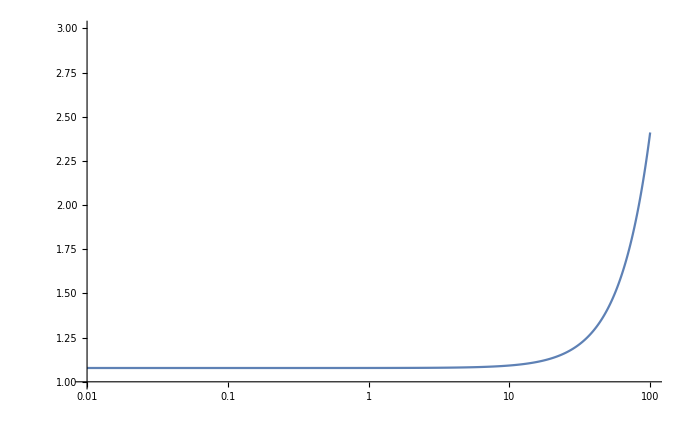

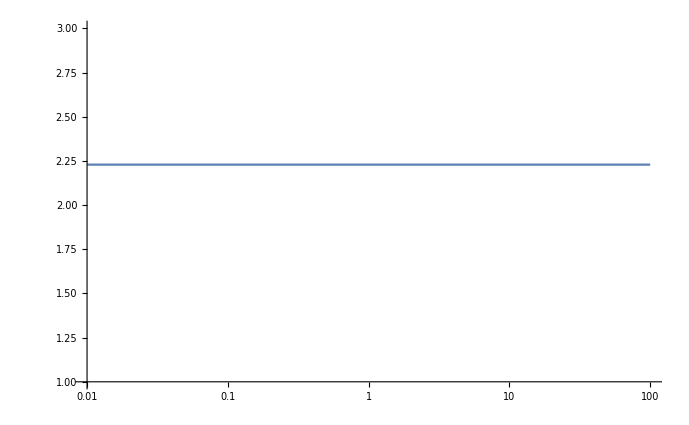

```mathematica
lpx=ListLogLinearPlot[pointsx,PlotRange->{{γpmin,γpmax},{1,3}},Joined->True]
lpy=ListLogLinearPlot[pointsy,PlotRange->{{γpmin,γpmax},{1,3}},Joined->True]
```

```mathematica
c2eqsimpl/.{γa->γa1}//FullSimplify
```

1/(1.15878×10^9+1. μ)μ^3 (384. √(90008.4+μ (-179864.+90000. μ))+μ (98304.+25. √(90008.4+μ (-179864.+90000. μ))+μ (0.0000915527+384. μ+1.5 √(90008.4+μ (-179864.+90000. μ)))))

```mathematica
ss=c2eqsimpl//FullSimplify//Chop//Solve[#==0,μ]&
```

{{μ→9.98623×10^-12 (-2.41419×10^12-5.00189×10^11 γp-0.000589163 √(1.81637×10^31+7.2462×10^30 γp+7.20695×10^29 γp^2))},{μ→9.98623×10^-12 (-2.41419×10^12-5.00189×10^11 γp+0.000589163 √(1.81637×10^31+7.2462×10^30 γp+7.20695×10^29 γp^2))}}

## ψ diffusion in linear polarization

```mathematica
EqPsiDrift=EqQs[[4]]/.{Qm->Q,Qp->Q,d->0}//FullSimplify[#,Assumptions->{Q>0}]&;
EqPsiNoise=Sqrt[(Dmatrix[[2,2]]+Dmatrix[[4,4]])]/2/.{Qm->Q,Qp->Q,d->0}//FullSimplify[#,Assumptions->{Q>0}]&;
dψ==EqPsiDrift dt+EqPsiNoise dW
```

dψ==(dW √((Csp (G+T) κ)/Q))/(√2)+dt γa Sin[2 ψ]

```mathematica
Cov[t_]:=EqPsiNoise^2/(2 Abs[2 γa])Exp[-Abs[2 γa] Abs[t]];
```

```mathematica
Cov[0]
```

(Csp (G+T) κ)/(8 Q Abs[γa])

```mathematica
newEqs=(EqQs/.{Qp-> Q+δQp,Qm-> Q+δQm})-(EqQs/.{Qp-> Q,Qm-> Q,ψ->0,d->0,G-> G0})//FullSimplify[#,Assumptions-> {Q>0}]&;
newEqs//MatrixForm
```

(2 (Q γa+(d+G-G0) (Csp+Q) κ+(-1+d+G) δQp κ-√((Q+δQm) (Q+δQp)) (γa Cos[2 ψ]+γp Sin[2 ψ]))
2 (Q γa-((d-G+G0) (Csp+Q)+(1+d-G) δQm) κ+√((Q+δQm) (Q+δQp)) (-γa Cos[2 ψ]+γp Sin[2 ψ]))
(2 (Q+δQm) (γp+(G-G0) α κ)-γp ((Q+δQm) √((Q+δQm)/(Q+δQp))+√((Q+δQm) (Q+δQp))) Cos[2 ψ]+γa ((Q+δQm) √((Q+δQm)/(Q+δQp))-√((Q+δQm) (Q+δQp))) Sin[2 ψ])/(2 (Q+δQm))
(2 d α (Q+δQm) κ+γp (-(Q+δQm) √((Q+δQm)/(Q+δQp))+√((Q+δQm) (Q+δQp))) Cos[2 ψ]+γa ((Q+δQm) √((Q+δQm)/(Q+δQp))+√((Q+δQm) (Q+δQp))) Sin[2 ψ])/(2 (Q+δQm))
γ (G0+2 G0 Q+d (δQm-δQp)-G (1+2 Q+δQm+δQp))
G γ (δQm-δQp)-d (γd+γ (2 Q+δQm+δQp)))

```mathematica
Gdsol=Solve[newEqs[[5;;6]]==0,{G,d}];
Gd={G,d}/.Gdsol[[1]];
dQs={δQp,δQm};
Gd1ord=Table[D[Gd[[i]],dQs[[j]]],{i,1,2},{j,1,2}]/.{δQp->0,δQm->0}//FullSimplify;
Gdlisub={G-> G0+Gd1ord[[1,1]]*δQp+Gd1ord[[1,2]]*δQm,d-> Gd1ord[[2,1]]*δQp+Gd1ord[[2,2]]*δQm};
```

```mathematica
QψEqs=newEqs[[{1,2,4}]]/.Gdlisub;
Qψvars={δQp,δQm,ψ};
QψlinEqs=Table[D[QψEqs[[i]],Qψvars[[j]]],{i,1,3},{j,1,3}]/.{δQp->0,δQm->0,ψ->0}//FullSimplify[#,Assumptions->Q>0]&;
QψlinEqs//MatrixForm
```

(-γa+2 (-1+G0) κ-(2 G0 (Csp+Q) (γ+4 Q γ+γd) κ)/((1+2 Q) (2 Q γ+γd)) | -γa+(2 G0 (Csp+Q) (γ-γd) κ)/((1+2 Q) (2 Q γ+γd)) | -4 Q γp
-γa+(2 G0 (Csp+Q) (γ-γd) κ)/((1+2 Q) (2 Q γ+γd)) | -γa-2 (1-G0+G0 (Csp+Q) (1/(1+2 Q)+γ/(2 Q γ+γd))) κ | 4 Q γp
γp/(2 Q)-(G0 α γ κ)/(2 Q γ+γd) | -γp/(2 Q)+(G0 α γ κ)/(2 Q γ+γd) | 2 γa)

```mathematica
mat1={
{1,1,0},
{1,-1,0},
{0,0,1}
};
linDrift=mat1.QψlinEqs.Inverse[mat1]//FullSimplify;
β=-linDrift[[2;;3,2;;3]]/.{G0->G};
linDrift//MatrixForm
mat1.Qψvars//MatrixForm
```

(-2 γa-(2 (1+(-1+2 Csp) G0+2 Q) κ)/(1+2 Q) | 0 | 0
0 | -(2 (2 (Csp G0+Q) γ+γd-G0 γd) κ)/(2 Q γ+γd) | -8 Q γp
0 | γp/(2 Q)-(G0 α γ κ)/(2 Q γ+γd) | 2 γa)

(δQm+δQp
-δQm+δQp
ψ)

```mathematica
β//MatrixForm
```

((2 (2 (Csp G+Q) γ+γd-G γd) κ)/(2 Q γ+γd) | 8 Q γp
-γp/(2 Q)+(G α γ κ)/(2 Q γ+γd) | -2 γa)

```mathematica
σ={{2Q,0},{0,1}}*Sqrt[2κ Csp (G+T)/Q];
```

```mathematica
stvars={ψ,δΔQ};
βmine={
{-2γa,α κ γ G/(γd+2Q γ)-γp/(2Q)},
{8Q γp, (2γ Q + 4 Csp γ G)/(γd+2Q γ)}};
σmine={{1,0},{0,2Q}}*Sqrt[2κ Csp (G+T)/Q];
```

```mathematica
βmine//MatrixForm
```

(-2 γa | -γp/(2 Q)+(G α γ κ)/(2 Q γ+γd)
8 Q γp | (4 Csp G γ+2 Q γ)/(2 Q γ+γd))

```mathematica
CharacteristicPolynomial[β,λ]//CoefficientList[#,λ]&//Reverse//FullSimplify
```

{1,2 γa-(2 (2 (Csp G+Q) γ+γd-G γd) κ)/(2 Q γ+γd),4 γp^2-(4 (γa (2 (Csp G+Q) γ+γd-G γd)+2 G Q α γ γp) κ)/(2 Q γ+γd)}

```mathematica
Disp=LyapunovSolve[β,σ.Transpose[σ]]//FullSimplify[#,Assumptions->{_Symbol∈Reals}]&;
Disp//MatrixForm
```

((2 Csp Q (G+T) (2 Q γ+γd) κ ((2 Q γ+γd) (γa^2+5 γp^2)-(γa (2 (Csp G+Q) γ+γd-G γd)+2 G Q α γ γp) κ))/((-(2 Q γ+γd) γp^2+γa (2 (Csp G+Q) γ+γd-G γd) κ+2 G Q α γ γp κ) (2 Q γ (γa-κ)-2 Csp G γ κ+γd (γa+(-1+G) κ))) | -(Csp (G+T) (2 Q γ+γd) κ (γa (2 Q γ+γd) γp-2 G Q α γ γa κ+4 (2 (Csp G+Q) γ+γd-G γd) γp κ))/(2 (-(2 Q γ+γd) γp^2+γa (2 (Csp G+Q) γ+γd-G γd) κ+2 G Q α γ γp κ) (2 Q γ (γa-κ)-2 Csp G γ κ+γd (γa+(-1+G) κ)))
-(Csp (G+T) (2 Q γ+γd) κ (γa (2 Q γ+γd) γp-2 G Q α γ γa κ+4 (2 (Csp G+Q) γ+γd-G γd) γp κ))/(2 (-(2 Q γ+γd) γp^2+γa (2 (Csp G+Q) γ+γd-G γd) κ+2 G Q α γ γp κ) (2 Q γ (γa-κ)-2 Csp G γ κ+γd (γa+(-1+G) κ))) | (Csp (G+T) κ (5 (2 Q γ+γd)^2 γp^2-4 (2 Q γ+γd) (γa (2 (Csp G+Q) γ+γd-G γd)+3 G Q α γ γp) κ+4 ((4 (Csp G+Q)^2+G^2 Q^2 α^2) γ^2-4 (-1+G) (Csp G+Q) γ γd+(-1+G)^2 γd^2) κ^2))/(8 Q (-(2 Q γ+γd) γp^2+γa (2 (Csp G+Q) γ+γd-G γd) κ+2 G Q α γ γp κ) (2 Q γ (γa-κ)-2 Csp G γ κ+γd (γa+(-1+G) κ))))

```mathematica
Disp[[1,1]]//FullSimplify[#,Assumptions->{Q>0,γ>0,γd>0,γa<0,G>0,α>0,κ>0,γp>0,T>0,Csp>0}]&
```

(2 Csp Q (G+T) (2 Q γ+γd) κ ((2 Q γ+γd) (γa^2+5 γp^2)-(γa (2 (Csp G+Q) γ+γd-G γd)+2 G Q α γ γp) κ))/((-(2 Q γ+γd) γp^2+γa (2 (Csp G+Q) γ+γd-G γd) κ+2 G Q α γ γp κ) (2 Q γ (γa-κ)-2 Csp G γ κ+γd (γa+(-1+G) κ)))

```mathematica
EqQs/.{Qp->Q,Qm-> Q,d->0,ψ-> 0}//FullSimplify[#,Assumptions->Q>0]&//MatrixForm
```

(2 Csp (G+T) κ-2 Q (γa+κ-G κ)
2 Csp (G+T) κ-2 Q (γa+κ-G κ)
-γp+(-1+G) α κ-ω
0
γ (-G (1+2 Q)+μ)
0)

```mathematica
qsub=Solve[(2 Csp (G+T) κ-2 Q (γa+κ-G κ)/.{G->μ/(1+2Q)})==0,Q]//FullSimplify;
```

```mathematica
Clear[α,κ,γ,γd,γp,γa,Nth,Ntr,T,μ,Csp]
```

```mathematica
α=5;
κ=300;
γ=1;
γd=50;
Nth=6.25*10^6;
Ntr=5.935*10^6;
T=Ntr/(Nth-Ntr);
μ=2;
Csp=10^-7;
γp=2π*200;
γa=-0.1;
```

```mathematica
Eigenvalues[β/.{G->μ/(1+2 Q)}/.qsub[[1]]]
β/.{G->μ/(1+2 Q)}/.qsub[[1]]//MatrixForm
```

{6.08545+2483.67 ⅈ,6.08545-2483.67 ⅈ}

(11.9709 | 5029.94
-1226.39 | 0.2)

```mathematica
Sqrt[Disp[[1,1]]]/.{G->μ/(1+2 Q)}/.qsub[[1]]
Sqrt[Disp[[2,2]]]/.{G->μ/(1+2 Q)}/.qsub[[1]]
```

0.0223333

0.0110278

```mathematica
(0.0118-0.010951375726315158)/0.0118
```

0.0719173

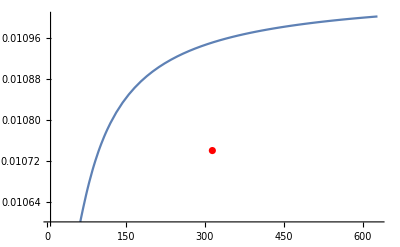

```mathematica
Clear[γp];
plth=Plot[Sqrt[Disp[[2,2]]]/.{G->μ/(1+2 Q)}/.qsub[[1]],{γp,2π*10,2π*100},PlotRange->{2π*{1,100},Full}];
Show[plth,plN]
```

```mathematica
NExpList={{62.8319,0.005006},{125.6637,0.0070266},{188.4956,0.0083079},{251.3274,0.0096052},{314.1593,0.010741},{376.9911,0.011702},{439.823,0.01219},{502.6548,0.012896},{565.4867,0.013812},{628.3185,0.013489}};
```

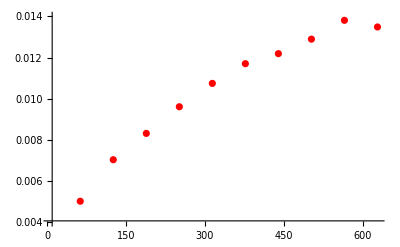

```mathematica
plN=ListPlot[NExpList,PlotStyle->Red,PlotRange->{2π*{1,100},{0.004,0.014}}]
```

```mathematica
NExpList
```

{{62.8319,0.005006},{125.664,0.0070266},{188.496,0.0083079},{251.327,0.0096052},{314.159,0.010741},{376.991,0.011702},{439.823,0.01219},{502.655,0.012896},{565.487,0.013812},{628.319,0.013489}}